# MATH299M/CMSC389W - Visualization through Mathematica Week 4: 2D Plotting

This week we start diving in to the more sophisticated plotting functions, powerful weapons in your visualization toolkit.

Modified Axis Plots

Briefly, we have available at our disposal plots such as LogPlot, LogLinearPlot, and LogLogPlot that allow us modify how functions are plotted. For example,

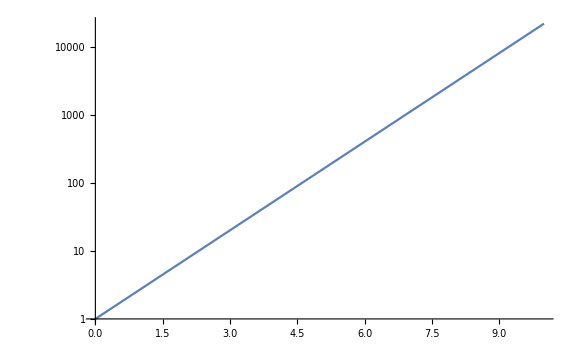

```mathematica
LogPlot[ⅇ^x,{x,0,10},ImageSize->Large]
```

Notice that in a LogPlot, ⅇ^x is actually linear! That’s because instead of plotting f(x), LogPlot plots log(f(x)). Similar rules apply for other axis modifying plots.

RegionPlot

RegionPlot highlights on the xy-plane just the points that you want. It takes three arguments, the first is a logical predicate in terms of two variables, something that will evaluate to True or False for each point in the plane, and then the next two arguments are domain tuples for those two variables, like the second argument of Plot. After that you can specify Options just like with Plot. RegionPlot works by sampling points in the plane, which can make it slow for complicated calculations, and often times it’s not very smooth when combined with Manipulate. We’ll learn a way to handle this later with Precalculation. You can use the PlotPoints option to specify the fineness of the grid used for the sampling - if your code is running slowly you can make this number smaller, or if you want a high resolution model you can make this number bigger.

Starting simple, here’s the region above the line y = x:

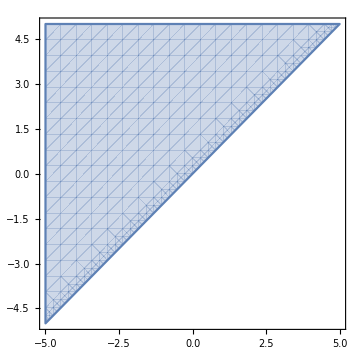

```mathematica
RegionPlot[y>x,{x,-5,5},{y,-5,5},ImageSize->Medium]
```

And here’s all points at most 1 from the origin *cough* the unit circle *cough* (and I changed the color):

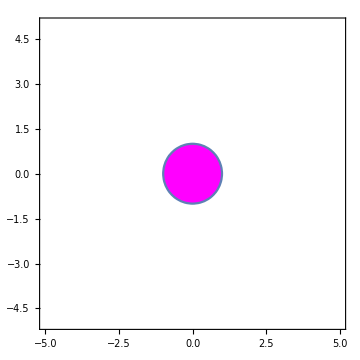

```mathematica
RegionPlot[Sqrt[x^2+y^2]≤1,{x,-5,5},{y,-5,5},ImageSize->Medium,PlotStyle->Magenta]
```

How about multiple regions, note it automatically colors them for us:

And legends exist so that you can make it for easy understanding!

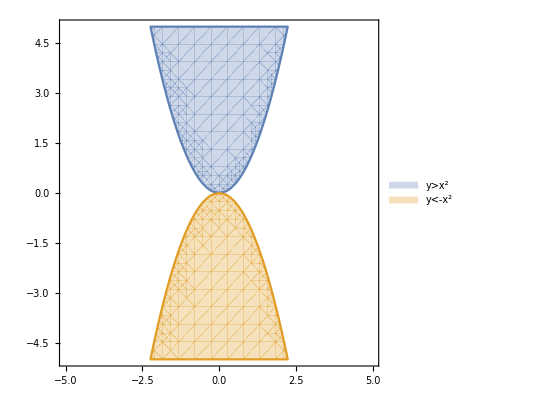

```mathematica
RegionPlot[{y>x^2,y<-x^2},{x,-5,5},{y,-5,5},PlotLegends->"Expressions"]
```

The shading can also overlap:

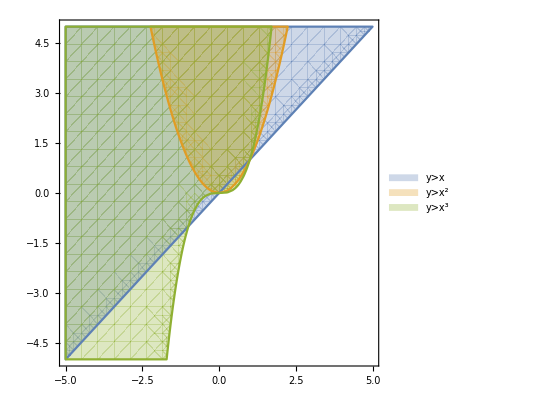

```mathematica
RegionPlot[{y>x,y>x^2,y>x^3},{x,-5,5},{y,-5,5},PlotLegends->"Expressions"]
```

Okay, let’s do something interesting now. Let’s make a function that take the product of x and y, rounds down, and then returns whether it’s a prime. That’ll have intuitive meaning, maybe, let’s see:

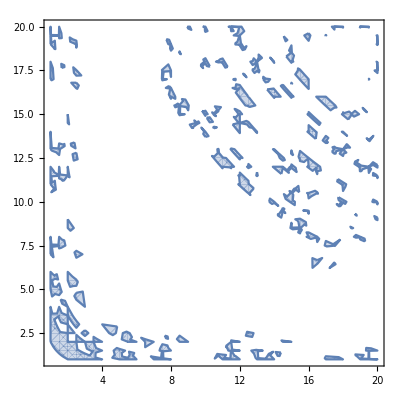

```mathematica
RegionPlot[{PrimeQ[Floor[x y]]},{x,1,20},{y,1,20}]
```

Less than clear what’s going on! And seems quite jagged. Let’s increase the PlotPoints and see if we can’t get a sensible image out of this.

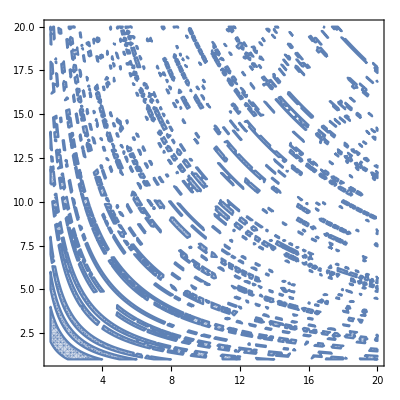

```mathematica
RegionPlot[{PrimeQ[Floor[x y]]},{x,1,20},{y,1,20},PlotPoints->50]
```

I have no idea what that means - but it’s super cool.

Okay, one more cool example, this one will use a logically complicated predicate. Don’t be scared of the x+ⅈy; if you haven’t seen a whole lot of complex analysis before, all you need to know here is that Sqrt[x^2+y^2] = Norm[x + ⅈy].

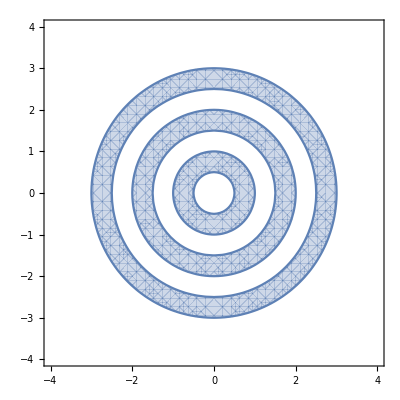

```mathematica
RegionPlot[(Norm[x+ⅈ y]>.5&&Norm[x+ⅈ y]<1)||(Norm[x+ⅈ y]>1.5&&Norm[x+ⅈ y]<2)||(Norm[x+ⅈ y]>2.5&&Norm[x+ⅈ y]<3),{x,-4,4},{y,-4,4}]
```

ContourPlot

ContourPlot is for drawing level sets of surfaces. If you haven’t taken multivariate calculus yet then you probably don’t know what this means, but we can explain. A surface is a function of two variables plotted in 3-space, that is, it’s a function f(x,y) that takes in an x value and a y value and spits out a number. You can think of this as a surface because if you have a 3d space with an x, y and z axis, and you plot the number f(x,y) on the z-axis for each x-y point, and the function is continuous, you get a smooth connected sheet floating above the xy plane (and, of course, passing below it whenever f is negative). Now, what if we take a plane parallel to the xy plane, so some function z = c where c is a constant, and plot where our surface intersects it? That’s exactly what a level set is. In general, the c level set of a function f(x,y) is the solution set to the equation f(x,y) = c, it’s all point (x,y) in the plane that map up to the value c on the surface. You should think of it as horizontal slices of the surface. ContourPlot takes three arguments - the first is an equation of the form f(x,y) = c, and the next two are domain tuples for the x and y variables, which, of course, can be any names you want besides “x” and “y”. ContourPlot also has our normal plot Options.

Horizontal slices of a cone should be easy to imagine, they’d be circles, so let’s start with that. An equation for a cone is f(x,y) = Sqrt[x^2+y^2]. If we take the level set c=2, then we’ll get the set of points in the xy plane for which Sqrt[x^2+y^2] = c, which is all points that are c from the origin, which is exactly the equation of a circle with radius c!

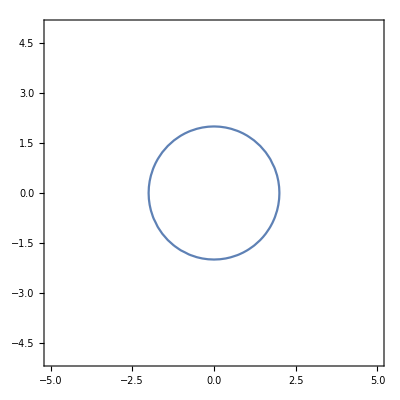

```mathematica
ContourPlot[Sqrt[x^2+y^2]==2,{x,-5,5},{y,-5,5}]
```

A pedagogical note - above the text doubled a motivation for our model and a teaching mechanism - if you haven’t seen level sets before then I’m sure you get the idea of them now, and even if you have seen them before you might already be getting a better grasp of them. This shows off just how suited Mathematica is for the classroom. It would be in-arguably useful to have this kind of tool when you’re trying to teach or learn multivariate calculus.

Okay, let’s do something more interesting now. Let’s plot a hyperboloid, which is a surface built up from hyperbolas (as you can guess by the fact that it’s function is f(x,y) = x^2-y^2, for which every level set is a hyperbola!):

```mathematica
Manipulate[ContourPlot[x^2-y^2==c,{x,-5,5},{y,-5,5},PlotPoints->40],{c,-5,5}]
```

And let' s plot a bunch of them at once because it’ll look cool:

```mathematica
Manipulate[ContourPlot[{x^2-y^2==-3c,x^2-y^2==-2c,x^2-y^2==c,x^2-y^2==c/2,x^2-y^2==c/3},{x,-5,5},{y,-5,5},PlotPoints->30],{c,-5,5}]
```

Okay, so, I mislead you a bit here. I sold ContourPlot to you as a tool from drawing level curves, which it is, but it can do more. If for the first argument instead of giving it an equation, we just give it an expression, that is, a function in terms of the two domain variables, then it’ll create a plot with colors that denote different value ranges of the surface, essentially a visualization of plotting all of the level curves at once. You can control the number of contours with Contours and then → followed by any number you want. One other fun Options is ColorFunction, which you set as a preset like “Rainbow”, or to a helper function you define, which should be a function of one variable that returns a color, in general you can use the RGBColor[·,·,·] function; it will feed the value of the first argument of ContourPlot into it for each x and y.

```mathematica
RedToBlue[val_]:=RGBColor[val,0,1/val];
GraphicsGrid[{{ContourPlot[Sqrt[x^2+y^2],{x,-5,5},{y,-5,5},PlotLegends->Automatic,ImageSize->300],ContourPlot[Sqrt[x^2+y^2],{x,-5,5},{y,-5,5},PlotLegends->Automatic,Contours->10,ColorFunction->RedToBlue,ImageSize->300],
ContourPlot[Sqrt[x^2+y^2],{x,-5,5},{y,-5,5},PlotLegends->Automatic,Contours->40,ColorFunction->"TemperatureMap",ImageSize->300]}},ImageSize->1200]
```

-Graphics-

Hyperbolic paraboloid/ saddle function/ Pringle’s chip

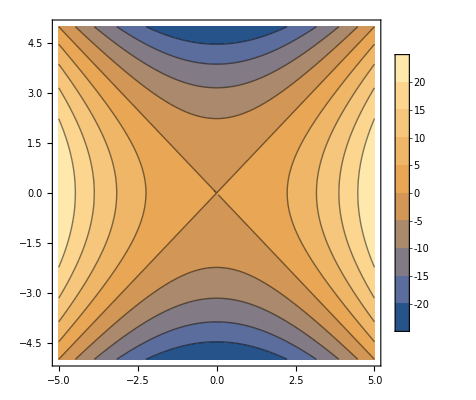

```mathematica
ContourPlot[x^2-y^2,{x,-5,5},{y,-5,5},PlotLegends->Automatic,PlotPoints->50]
```

Okay this next one is going to be ridiculously cool if you understand the physics behind it: total energy of a simply harmonic oscillator

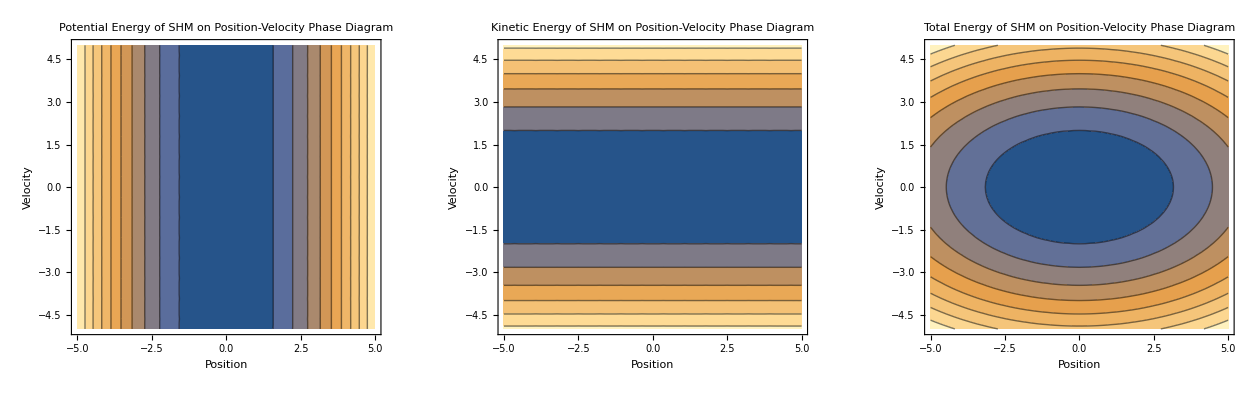

```mathematica
k=.4; (* Spring Constant *)
m=1; (* Mass *)
u[x_]:=1/2 m k x^2; (* Potential Energy of mass on spring *)
ke[x_]:=1/2 m v^2; (* Kinetic Energy of mass on spring *)
GraphicsGrid[{{ContourPlot[u[x],{x,-5,5},{v,-5,5},FrameLabel->{"Position","Velocity"},PlotLabel->"Potential Energy of SHM on Position-Velocity Phase Diagram"],
ContourPlot[ke[x],{x,-5,5},{v,-5,5},FrameLabel->{"Position","Velocity"},PlotLabel->"Kinetic Energy of SHM on Position-Velocity Phase Diagram"],
ContourPlot[ke[x]+u[x],{x,-5,5},{v,-5,5},FrameLabel->{"Position","Velocity"},PlotLabel->"Total Energy of SHM on Position-Velocity Phase Diagram"]}},ImageSize->1250]
```

Note: blue is lower energy, yellow is higher energy

On the left, our potential energy increases as our displacement (horizontal axis) increases from equilibrium (0); however, the velocity of the mass does not affect its potential energy. 
In the middle, our kinetic energy increases with velocity (the vertical axis) but does not change if the position of the mass changes.
Bringing the two together, we get ellipses! What does this mean? Well, the contours are one-dimensional regions of equal value, so each ellipse describes the set of values where the total energy of the spring-mass system are equal. In an isolated and optimal spring-mass system, the total energy should never change. A spring-mass system oscillating changes position and velocity over time, so if we start a spring, one one of the contours, the position and velocity will follow the contour because the energy must necessarily stay the same!
The shaded ellipse in the middle of the rightmost image is just because ContourPlot on a function groups together ranges of level sets, so really you can think of that ellipse as a dense stack of ellipses that shrink all the way down to the trivial ellipse, a point at the origin, a simple harmonic oscillator with 0 total energy.

DensityPlot

Now that you know ContourPlot, DensityPlot should be easy to use and understand. DensityPlot is what happens when you take the Contour Option towards infinity in CountourPlot, that is, instead of showing color coded levels of the function of two variables it shows a continuous gradient of the value. Just as ContourPlot does, it takes in three arguments, the first being a function of two variables, and the next two being domain tuples for those two variables. Normal Options apply. Below we’ll compare ContourPlot’s and DensityPlot’s of the same function.

```mathematica
GraphicsGrid[{{ContourPlot[x^2+y^2,{x,-10,10},{y,-10,10},Contours->10,ColorFunction->"SunsetColors",PlotLegends->Automatic,ImageSize->270],
ContourPlot[x^2+y^2,{x,-10,10},{y,-10,10},Contours->30,ColorFunction->"SunsetColors",PlotLegends->Automatic,ImageSize->270],DensityPlot[x^2+y^2,{x,-10,10},{y,-10,10},ColorFunction->"SunsetColors",PlotLegends->Automatic,ImageSize->270]}},ImageSize->1100]
```

-Graphics-

PolarPlot

PolarPlot takes two arguments. The first is a function for the radius in terms of some variable, and the second is a domain tuple for that variable, generally chosen to be θ, and then it draws the function (r(θ),θ) plotted on a polar graph. Recall that a polar graph is one where the grid lines are concentric circles with perpendicular radial lines rather than an xy grid - the axes we are using, instead of x from -∞ to ∞ and y from -∞ to ∞ are r from 0 to ∞ and θ from 0 to 2π, radius and angle, respectively. You could also think of it as r from -∞ to ∞ ad θ from 0 to π, both cover the negative direction - in general with PolarPlot you can have any value of r and θ, so you can combine these notions of the opposite direction being represented by a negative radius and by an angle between π and 2π, and also you can utilize values of θ above 2π and below 0 to wrap around the origin more, although on principle you should be able to draw every polar curve you can imagine on the domain [0,∞)x[0,2π).

A circle in polar form is extremely simple - the radius is constant and theta swings through all angles.

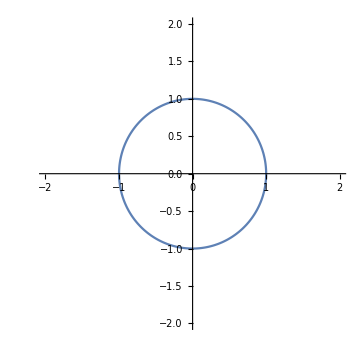

```mathematica
PolarPlot[1,{θ,0,2π},PlotRange->2,AspectRatio->1,ImageSize->Medium]
```

The polar flowers are always a go-to:

```mathematica
Manipulate[PolarPlot[Sin[n θ],{θ,0,2π},PlotRange->2,AspectRatio->1,ImageSize->Medium],{{n,3},1,10,1}]
```

Something crazy to see, and very illuminating as to how these flowers are actually drawn, is if you let n be any real number:

```mathematica
Manipulate[PolarPlot[Sin[n θ],{θ,0,2π},PlotRange->2,AspectRatio->1,ImageSize->Medium],{{n,3},-10,10}]
```

The trig functions do simple things on polar graphs - why this is is important and interesting, and these tools are particularly conducive to understanding why. I insist that you play with these yourself and build an understanding of how polar flowers, cardioids, and conics are drawn in polar form. I cheated a little bit adding a tiny bit (denoted epsilon ϵ) to the start and end of the θ interval - otherwise we have dividing by zero problems and errors get thrown (which function(s) is this a problem for?).

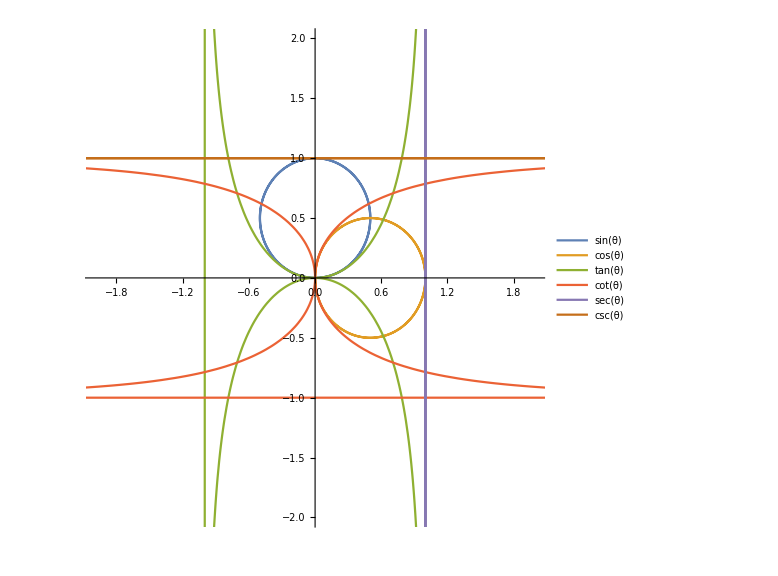

```mathematica
ϵ=.0001;
PolarPlot[{Sin[θ],Cos[θ],Tan[θ],Cot[θ],Sec[θ],Csc[θ]},{θ,0+ϵ,2π-ϵ},PlotRange->2,AspectRatio->1,ImageSize->Large,PlotLegends->"Expressions"]
```

ParametricPlot

ParametricPlot is one of my favorite tools in Mathematica - it’s extremely powerful. In case you’ve never seen parametric curves before (multivariate calculus is usually the first time you see such a thing), the idea is that you draw an arbitrary curve in the plane and parameterize it with a real number t, that is, you have a function f(t) that returns a coordinate pair (x(t),y(t)) that varies with t. ParameticPlot takes two or three arguments, the first is a tuple in terms of t that describes the path in the plane, and the second is a tuple that gives the domain of t, and of course “t” can be any variable, and we have the normal Plot options, if we don’t use the third argument. Notice that in this case there is only one dimension of domain as for a parameterized line it can be fully described as a function from ℝ to ℝ^2. If we use the third argument, it’s another domain tuple, so actually we may construct a parametric function {x(t,s),y(t,s)} that swings through all points (x,y) ∈ ℝ^2 wrt to all specified values of s and t (or whatever you call these variables, often it’s nice to call them θ and r if you’re doing something polar).

Let’s see something you can’t do with a Plot, plotting something that isn’t a function, that is, doesn’t pass the vertical line test:

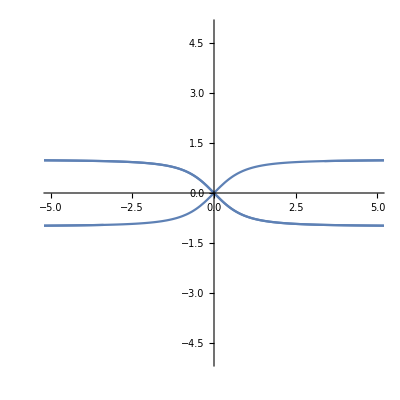

```mathematica
ParametricPlot[{Tan[t],Sin[t]},{t,-5,5},PlotRange->5,AspectRatio->1]
```

If you want a normal function, you can type {t,f[t]} for {x(t),y(t)}, which is equivalent to using Plot on f[t] where t is the dependent variable. Similarly if we make the second element of the tuple just t and the first f[t], then it’s like we’re plotting on the graph x = y, like what Plot does but with the axes flipped.

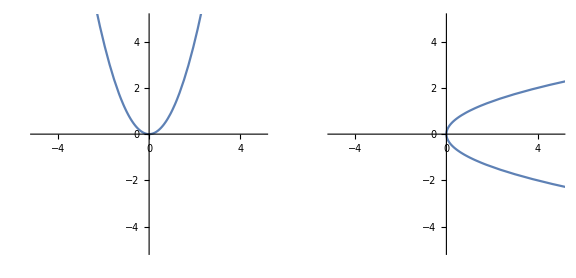

```mathematica
GraphicsGrid[{{ParametricPlot[{t,t^2},{t,-5,5},PlotRange->5,AspectRatio->1],ParametricPlot[{t^2,t},{t,-5,5},PlotRange->5,AspectRatio->1]}},ImageSize->Large]
```

ParametricPlot is great for Polar drawings as you can parameterize the radius and angle:

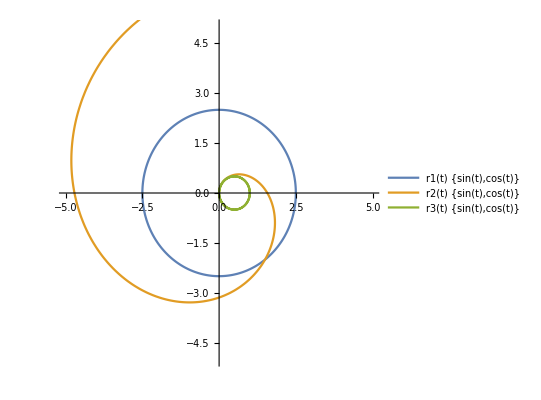

```mathematica
r1[t_]:=2.5; (* Constant Radius *)
r2[t_]:=t; (* Increasing Radius *)
r3[t_]:=Sin[t]; (* Sinusoidal Radius *)
ParametricPlot[{r1[t]{Sin[t],Cos[t]},r2[t]{Sin[t],Cos[t]},r3[t]{Sin[t],Cos[t]}},{t,0,2π},PlotRange->5,AspectRatio->1,PlotLegends->"Expressions"]
```

ParametricPlot with two domain variables, possibly combined with this polar technique, is great for the objects we want to integrate over in Calculus II, like washers and wedges:

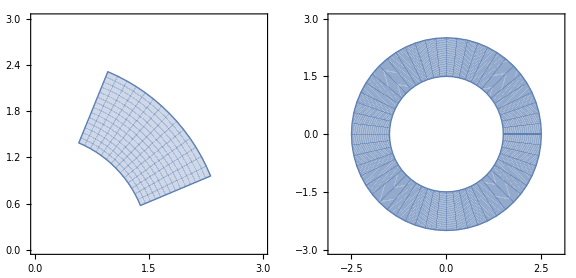

```mathematica
GraphicsGrid[{{ParametricPlot[r{Cos[θ],Sin[θ]},{r,1.5,2.5},{θ,π/8,(3π)/8},PlotRange->{{0,3},{0,3}},AspectRatio->1],
ParametricPlot[r{Cos[θ],Sin[θ]},{r,1.5,2.5},{θ,0,2π},PlotRange->3,AspectRatio->1]}},ImageSize->Large]
```

One more trick to show you is using Manipulate on the domain to control the drawing:

```mathematica
Manipulate[ParametricPlot[Sin[2θ]{Sin[θ],Cos[θ]},{θ,min,max},PlotRange->1.5,AspectRatio->1],{{min,0},-2π,0},{{max,π/8},0,2π}]
```

You now have at your disposal powerful tools to draw arbitrary curves in the plane!

One caution about Parametric and Polar Plot. They seem to perform worse than their other counterparts, so be careful when using them.

Discrete and List Plots

Sometimes we aren’t interested in plotting continuous functions. If you ever have discrete data, we plot them using a variety of List Plots and Discrete Plots

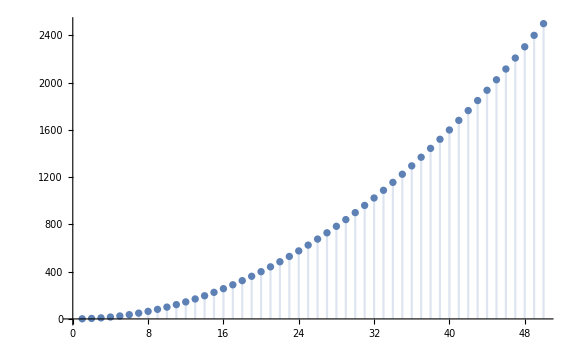

```mathematica
DiscretePlot[k^2,{k,1,50},ImageSize->Large]
```

We can also arbitrarily change the step interval or even the values at which the discrete values of the function are plotted.

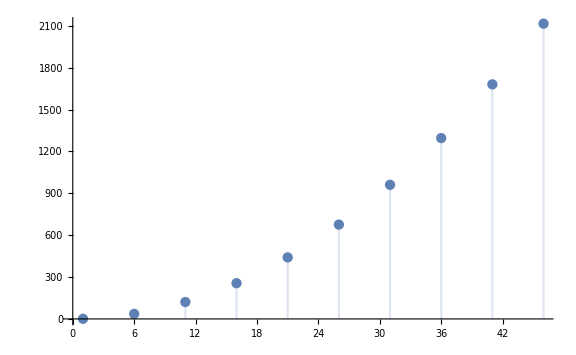

```mathematica
DiscretePlot[k^2,{k,1,50,5},ImageSize->Large]
```

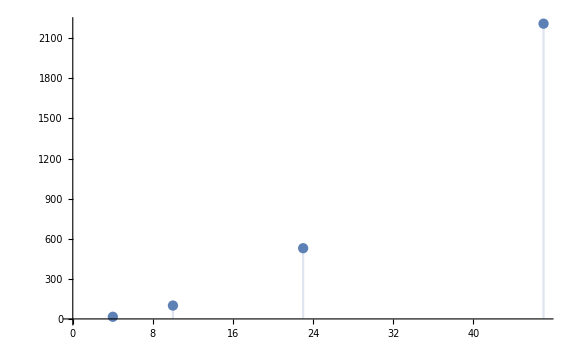

```mathematica
DiscretePlot[k^2,{k,{4,10,23,47}},ImageSize->Large]
```

Perhaps you do not have the exact function that expresses your data. We can use list plot to plot arbitrary lists of data. The first argument to ListPlot are the y values of the data as a list.

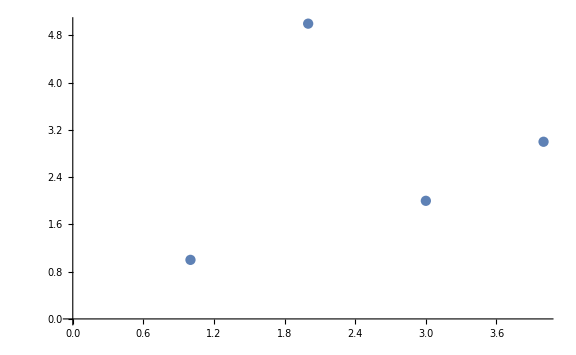

```mathematica
ListPlot[{1,5,2,3},ImageSize->Large]
```

Use of a list of pairs allows us to also control the x values of the data.

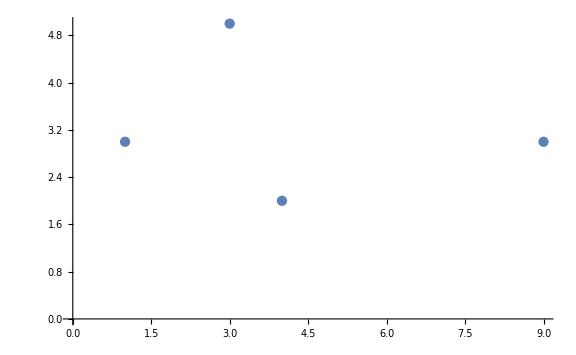

```mathematica
ListPlot[{{1,3},{3,5},{4,2},{9,3}},ImageSize->Large]
```

Both plots have many more options not covered in this or the previous lesson. Make sure to check out their doc pages for more ways to use them, including labeling points, changing point style, usage for Riemann Approximations, coloring, and others.

## Ajeet Gary - Formerly University of Maryland Experimental Geometry Lab Dan Zou - University of Maryland Computer Science Department MATH299M/CMSC389W Spring 2020 February 28th, 2020

## Vlad Dobrin - University of Maryland Computer Science MATH299M/CMSC389W Spring 2020 May 29th, 2020